```mathematica
Clear[Evaluate[Context[]<>"*"]]

(* Here is fake signal data. *)
ω={0.1325,0.3275,0.754,0.9600,0.4900};
A={1.0, 0.001, 0.2, 6.1, 0.1};
ϕ={2.090, 1.090, 0.000, 1.234, 2.034};
NN=1024;

proj[u_,v_]:=Sum[Conjugate[u[t]]×v[t],{t,0,NN-1}]/NN;  (* project u onto v *)
easyInt[ωj_,ωk_]:=If[ωj==ωk,NN-1,-ⅈ/(2π(-ωj+ωk))(1-Exp[-ⅈ 2π(-ωj+ωk)(NN-1)])];

(* v are the individual components of the signal.*)
v1[t_]:=A[[1]]Exp[-ⅈ (2π ω[[1]] t+ϕ[[1]])];
v2[t_]:=A[[2]]Exp[-ⅈ (2π ω[[2]] t+ϕ[[2]])];
v3[t_]:=A[[3]]Exp[-ⅈ (2π ω[[3]] t+ϕ[[3]])];
v4[t_]:=A[[4]]Exp[-ⅈ (2π ω[[4]] t+ϕ[[4]])];
v5[t_]:=A[[5]]Exp[-ⅈ (2π ω[[5]] t+ϕ[[5]])];
signal[t_]:=v1[t]+v2[t]+v3[t]+v4[t]+v5[t];


(* In actual implementation, e1 is a complex sinusoidal with frequency component
determined by first estimating with interpolated FFT, then refined by applying a
maximizing the projection of u1 onto the signal.  Same applies to e2, e3, ...
In this mock-up, the frequency is simply copied. *)

(* As said above, assume ω[[1]] was found through a FFT and refinement process. *)
(* en are the frequency component.  u1 are the orthogonalized counterpart. *)
e1[t_]:=Exp[-ⅈ 2π ω[[1]] t];
u1[t_]:=e1[t];

e2[t_]:=Exp[-ⅈ 2π ω[[2]]t];
p21=proj[u1,e2];
u2[t_]:=e2[t]-p21 u1[t];

e3[t_]:=Exp[-ⅈ 2π ω[[3]]t];
p31=proj[u1,e3];
u31[t_]:=e3[t]-p31 u1[t];
p32=proj[u2,u31];
u3[t_]:=u31[t]-p32 u2[t];

e4[t_]:=Exp[-ⅈ 2π ω[[4]]t];
p41=proj[u1,e4];
u41[t_]:=e4[t]-p41 u1[t];
p42=proj[u2,u41];
u42[t_]:=u41[t]-p42 u2[t];
p43=proj[u3,u42];
u4[t_]:=u42[t]-p43 u3[t];

e5[t_]:=Exp[-ⅈ 2π ω[[5]]t];
p51=proj[u1,e5];
u51[t_]:=e5[t]-p51 u1[t];
p52=proj[u2,u51];
u52[t_]:=u51[t]-p52 u2[t];
p53=proj[u3,u52];
u53[t_]:=u52[t]-p53 u3[t];
p54=proj[u4,u53];
u5[t_]:=u53[t]-p54 u4[t]

Print["1-<u1|u1> = ",1-proj[u1,u1]]
Print["1-<u2|u2> = ",1-proj[u2,u2]]
Print["1-<u3|u3> = ",1-proj[u3,u3]]
Print["1-<u4|u4> = ",1-proj[u4,u4]]
Print["1-<u5|u5> = ",1-proj[u5,u5]]
Print["<u1|u2> = ",proj[u1,u2]]
Print["<u1|u3> = ",proj[u1,u3]]
Print["<u2|u3> = ",proj[u2,u3]]
Print["<u1|u4> = ",proj[u1,u4]]
Print["<u2|u4> = ",proj[u2,u4]]
Print["<u3|u4> = ",proj[u3,u4]]
Print["<u1|u5> = ",proj[u1,u5]]
Print["<u2|u5> = ",proj[u2,u5]]
Print["<u3|u5> = ",proj[u3,u5]]
Print["<u4|u5> = ",proj[u4,u5]]

(*Plot[{Re[u1[t]],Im[u1[t]],Re[u2[t]],Im[u2[t]],Re[u3[t]],Im[u3[t]],Re[u4[t]],Im[u4[t]],Re[u5[t]],Im[u5[t]]},{t,0,1}]*)
```

1-<u1|u1> = 0.+0. ⅈ

1-<u2|u2> = 2.05626×10^-6+0. ⅈ

1-<u3|u3> = 1.58154×10^-6+0. ⅈ

1-<u4|u4> = 3.83381×10^-6+0. ⅈ

1-<u5|u5> = 5.57929×10^-6+0. ⅈ

<u1|u2> = -2.92735×10^-18+2.49366×10^-18 ⅈ

<u1|u3> = -4.06576×10^-18-8.67362×10^-19 ⅈ

<u2|u3> = 8.58792×10^-10-1.25941×10^-9 ⅈ

<u1|u4> = -2.60209×10^-18+2.22261×10^-18 ⅈ

<u2|u4> = 1.83859×10^-9-2.7642×10^-10 ⅈ

<u3|u4> = -3.07444×10^-10-3.31544×10^-10 ⅈ

<u1|u5> = 1.38236×10^-18+5.96311×10^-18 ⅈ

<u2|u5> = 2.86838×10^-9-2.65151×10^-9 ⅈ

<u3|u5> = 1.77363×10^-9+4.0817×10^-10 ⅈ

<u4|u5> = 2.3907×10^-9-1.62472×10^-9 ⅈ

#### Method 1 : Project each basis component onto the full signal, then subtract.

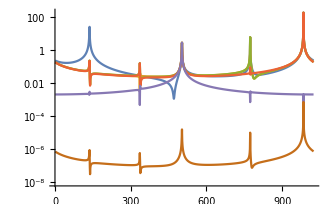

```mathematica
a1=Conjugate[proj[signal,u1]];
a2=Conjugate[proj[signal,u2]];
a3=Conjugate[proj[signal,u3]];
a4=Conjugate[proj[signal,u4]];
a5=Conjugate[proj[signal,u5]];
sampledSignal=Table[signal[t],{t,0,NN-1}];
sample2=Table[signal[t]-a1 u1[t],{t,0,NN-1}];
sample3=Table[signal[t]-a1 u1[t]-a2 u2[t],{t,0,NN-1}];
sample4=Table[signal[t]-a1 u1[t]-a2 u2[t]-a3 u3[t],{t,0,NN-1}];
sample5=Table[signal[t]-a1 u1[t]-a2 u2[t]-a3 u3[t]-a4 u4[t],{t,0,NN-1}];
sample6=Table[signal[t]-a1 u1[t]-a2 u2[t]-a3 u3[t]-a4 u4[t]-a5 u5[t],{t,0,NN-1}];
ftOrig=Fourier[sampledSignal];
ft2=Fourier[sample2];
ft3=Fourier[sample3];
ft4=Fourier[sample4];
ft5=Fourier[sample5];
ft6=Fourier[sample6];
ListLogPlot[{Abs[ftOrig],Abs[ft2],Abs[ft3],Abs[ft4],Abs[ft5],Abs[ft6]},PlotRange->{Full,Full},Joined->True]
```

#### Method 2 : Project then subtract, project then subtract.

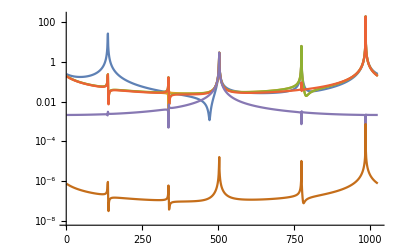

```mathematica
a1=Conjugate[proj[signal,u1]];
a2=Conjugate[proj[signal[#]-a1 u1[#]&,u2]];
a3=Conjugate[proj[signal[#]-a1 u1[#]-a2 u2[#]&,u3]];
a4=Conjugate[proj[signal[#]-a1 u1[#]-a2 u2[#]-a3 u3[#]&,u4]];
a5=Conjugate[proj[signal[#]-a1 u1[#]-a2 u2[#]-a3 u3[#]-a4 u4[#]&,u5]];
sampledSignal=Table[signal[t],{t,0,NN-1}];
sample2=Table[signal[t]-a1 u1[t],{t,0,NN-1}];
sample3=Table[signal[t]-a1 u1[t]-a2 u2[t],{t,0,NN-1}];
sample4=Table[signal[t]-a1 u1[t]-a2 u2[t]-a3 u3[t],{t,0,NN-1}];
sample5=Table[signal[t]-a1 u1[t]-a2 u2[t]-a3 u3[t]-a4 u4[t],{t,0,NN-1}];
sample6=Table[signal[t]-a1 u1[t]-a2 u2[t]-a3 u3[t]-a4 u4[t]-a5 u5[t],{t,0,NN-1}];
ftOrig=Fourier[sampledSignal];
ft2=Fourier[sample2];
ft3=Fourier[sample3];
ft4=Fourier[sample4];
ft5=Fourier[sample5];
ft6=Fourier[sample6];
ListLogPlot[{Abs[ftOrig],Abs[ft2],Abs[ft3],Abs[ft4],Abs[ft5],Abs[ft6]},PlotRange->{Full,Full},Joined->True]
```

#### Cruft

```mathematica
ft3=Fourier[sample3];
```

```mathematica
sample3=Table[signal[t]-Conjugate[a1] u1[t]-Conjugate[a2]u2[t],{t,0,NN-1}];
```

```mathematica
Nfreqs=3;
data=Table[Sum[A[[j]]Exp[-ⅈ(2π ω[[j]](i-1)+ϕ[[j]])],{j,1,Nfreqs}],{i,1,NN}];

dataOrig=data;
e1disc=Table[f1[i],{i,0,NN-1}];
e2disc=Table[f2[i],{i,0,NN-1}];
e3disc=Table[f3[i],{i,0,NN-1}];

projection1=Sum[data[[i]]**e1disc[[i]],{i,1,NN}];
component1=Table[projection1**e1disc[[i]],{i,1,NN}];
data=data-component1;
data1 = data;

Print["Projeciton Amplitude 1: ",projection1]
Print["Check Projection Amplitude 1: ",Sum[data[[i]]**e1disc[[i]],{i,1,NN}]]

projection2=Sum[data[[i]]**e2disc[[i]],{i,1,NN}];
component2=Table[projection2**e2disc[[i]],{i,1,NN}];
data=data-component2;
data2 = data;

Print["Projection Amplitude 2: ",projection2]
Print["Check Projection Amplitude 1: ",Sum[data[[i]]**e1disc[[i]],{i,1,NN}]]
Print["Check Projection Amplitude 2: ",Sum[data[[i]]**e2disc[[i]],{i,1,NN}]]

projection3=Sum[data[[i]]**e3disc[[i]],{i,1,NN}];
component3=Table[projection3**e3disc[[i]],{i,1,NN}];
data=data-component3;
data3=data;

Print["Projection Amplitude 3: ",projection3]
Print["Check Projection Amplitude 1: ",Sum[data[[i]]**e1disc[[i]],{i,1,NN}]]
Print["Check Projection Amplitude 2: ",Sum[data[[i]]**e2disc[[i]],{i,1,NN}]]
Print["Check Projection Amplitude 3: ",Sum[data[[i]]**e3disc[[i]],{i,1,NN}]]

projection1a=Sum[data[[i]]**e1disc[[i]],{i,1,NN}];
component1a=Table[projection1a**e1disc[[i]],{i,1,NN}];
data=data-component1a;
data1a = data;

Print["Projeciton Amplitude 1a: ",projection1a]
Print["Check Projection Amplitude 1: ",Sum[data[[i]]**e1disc[[i]],{i,1,NN}]]
Print["Check Projection Amplitude 2: ",Sum[data[[i]]**e2disc[[i]],{i,1,NN}]]
Print["Check Projection Amplitude 3: ",Sum[data[[i]]**e3disc[[i]],{i,1,NN}]]

projection2a=Sum[data[[i]]**e2disc[[i]],{i,1,NN}];
component2a=Table[projection2a**e2disc[[i]],{i,1,NN}];
data=data-component2a;
data2a = data;

Print["Projeciton Amplitude 2a: ",projection2a]
Print["Check Projection Amplitude 1: ",Sum[data[[i]]**e1disc[[i]],{i,1,NN}]]
Print["Check Projection Amplitude 2: ",Sum[data[[i]]**e2disc[[i]],{i,1,NN}]]
Print["Check Projection Amplitude 3: ",Sum[data[[i]]**e3disc[[i]],{i,1,NN}]]

projection3a=Sum[data[[i]]**e3disc[[i]],{i,1,NN}];
component3a=Table[projection3a**e3disc[[i]],{i,1,NN}];
data=data-component3a;
data3a = data;

Print["Projeciton Amplitude 3a: ",projection3a]
Print["Check Projection Amplitude 1: ",Sum[data[[i]]**e1disc[[i]],{i,1,NN}]]
Print["Check Projection Amplitude 2: ",Sum[data[[i]]**e2disc[[i]],{i,1,NN}]]
Print["Check Projection Amplitude 3: ",Sum[data[[i]]**e3disc[[i]],{i,1,NN}]]

projection1b=Sum[data[[i]]**e1disc[[i]],{i,1,NN}];
component1b=Table[projection1b**e1disc[[i]],{i,1,NN}];
data=data-component1b;
data1b = data;

Print["Projeciton Amplitude 1b: ",projection1b]
Print["Check Projection Amplitude 1: ",Sum[data[[i]]**e1disc[[i]],{i,1,NN}]]
Print["Check Projection Amplitude 2: ",Sum[data[[i]]**e2disc[[i]],{i,1,NN}]]
Print["Check Projection Amplitude 3: ",Sum[data[[i]]**e3disc[[i]],{i,1,NN}]]

projection2b=Sum[data[[i]]**e2disc[[i]],{i,1,NN}];
component2b=Table[projection2b**e2disc[[i]],{i,1,NN}];
data=data-component2b;
data2b = data;

Print["Projeciton Amplitude 2b: ",projection2b]
Print["Check Projection Amplitude 1: ",Sum[data[[i]]**e1disc[[i]],{i,1,NN}]]
Print["Check Projection Amplitude 2: ",Sum[data[[i]]**e2disc[[i]],{i,1,NN}]]
Print["Check Projection Amplitude 3: ",Sum[data[[i]]**e3disc[[i]],{i,1,NN}]]
```

Projeciton Amplitude 1: -15.9203+27.8157 ⅈ

Check Projection Amplitude 1: 0.0155623-0.0271903 ⅈ

Projection Amplitude 2: 14.8094+28.3898 ⅈ

Check Projection Amplitude 1: 0.0111345-0.0246082 ⅈ

Check Projection Amplitude 2: -0.014484-0.027766 ⅈ

Projection Amplitude 3: 6.40315-0.0000175742 ⅈ

Check Projection Amplitude 1: 0.00439224-0.0195293 ⅈ

Check Projection Amplitude 2: -0.0149869-0.0285035 ⅈ

Check Projection Amplitude 3: -0.00626319+1.71901×10^-8 ⅈ

Projeciton Amplitude 1a: 0.00439224-0.0195293 ⅈ

Check Projection Amplitude 1: -4.29349×10^-6+0.0000190903 ⅈ

Check Projection Amplitude 2: -0.01499-0.0285043 ⅈ

Check Projection Amplitude 3: -0.00628331+0.0000170971 ⅈ

Projeciton Amplitude 2a: -0.01499-0.0285043 ⅈ

Check Projection Amplitude 1: 1.51262×10^-7+0.0000164785 ⅈ

Check Projection Amplitude 2: 0.0000146606+0.000027878 ⅈ

Check Projection Amplitude 3: -0.00627885+0.0000176093 ⅈ

Projeciton Amplitude 3a: -0.00627885+0.0000176093 ⅈ

Check Projection Amplitude 1: 6.74872×10^-6+0.0000114797 ⅈ

Check Projection Amplitude 2: 0.0000151557+0.0000285997 ⅈ

Check Projection Amplitude 3: 6.14162×10^-6-1.72244×10^-8 ⅈ

Projeciton Amplitude 1b: 6.74872×10^-6+0.0000114797 ⅈ

Check Projection Amplitude 1: -6.59699×10^-9-1.12216×10^-8 ⅈ

Check Projection Amplitude 2: 0.0000151576+0.0000285987 ⅈ

Check Projection Amplitude 3: 6.14362×10^-6-3.46651×10^-8 ⅈ

Projeciton Amplitude 2b: 0.0000151576+0.0000285987 ⅈ

Check Projection Amplitude 1: -1.10556×10^-8-8.58223×10^-9 ⅈ

Check Projection Amplitude 2: -1.48246×10^-8-2.79704×10^-8 ⅈ

Check Projection Amplitude 3: 6.13913×10^-6-3.51653×10^-8 ⅈ

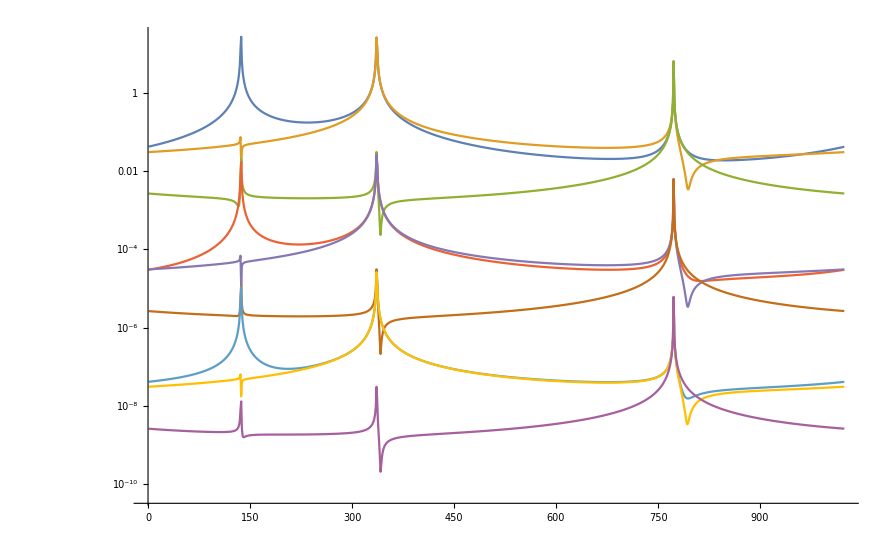

```mathematica
ftOrig=Fourier[dataOrig];
ft1=Fourier[data1];
ft2=Fourier[data2];
ft3=Fourier[data3];
ft1a=Fourier[data1a];
ft2a=Fourier[data2a];
ft3a=Fourier[data3a];
ft1b=Fourier[data1b];
ft2b=Fourier[data2b];
ListLogPlot[{Abs[ftOrig],Abs[ft1],Abs[ft2],Abs[ft3],Abs[ft1a],Abs[ft2a],Abs[ft3a],Abs[ft1b], Abs[ft2b]},PlotRange->{Full,Full},Joined->True]
```

-18.

710.411

0.

0.0589872

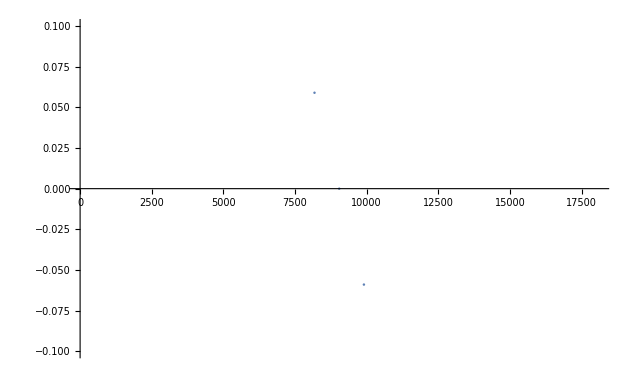

```mathematica
ωa=39.408290474;
ωb=10.733638813;
ω1=39.467277630;
list=Flatten[Table[l ωa+k ωb-m ω1,{l,-10,10},{k,-10,10},{m,-20,20}]];
-ω1+2ωb
RankedMin[Abs[list],1]
RankedMin[Abs[list],2]
ListPlot[list,PlotRange-> {Full,{-0.1,0.1}}]
```